Dimitriou Eleftherios
AEM: 4399

# Project 1: Solving Kepler’s Equation: M = E - esin(E), e<1

Task 1: Newton Raphson method

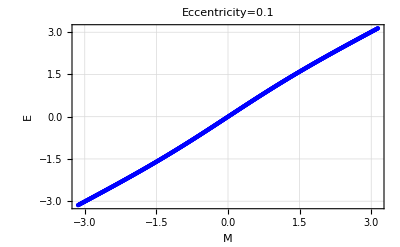

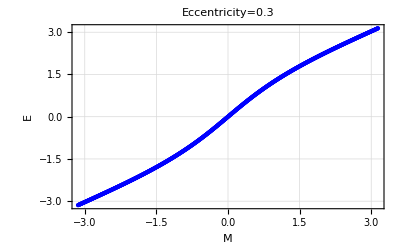

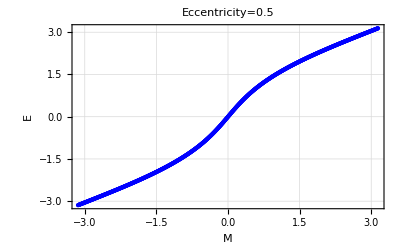

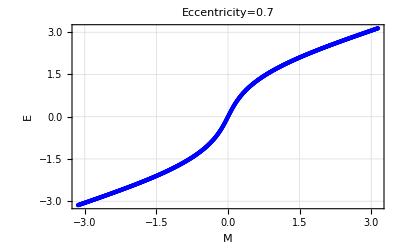

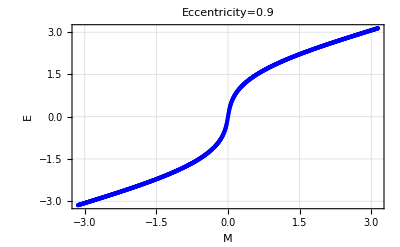

```mathematica
mydatamatrix = {};
etable = Table[l,{l,0.1,0.9,0.2}] ;(* pinakas me tis zhtoumenes ekkentrothtes *)
epsilon=100;

Do[
For[i=0,i<1000,i++,
M=-Pi+2*Pi*N[i/999]; (* diamerhsh tou diasthmatos apo -pi ews pi gia na parw kai tis arnhtikes times sto diagramma kai gia na paroume to sunoliko diasthma 2*pi *)
Ei=M;                                     (* arxikh sunthikh se kathe epanalhpsh *)
While[epsilon>N[10^(-4)], (* epilogh sfalmatos -> error = 0.0001 *)
Eiplus1 = N[Ei-(Ei-etable[[m]]*Sin[Ei]-M)/(1-etable[[m]]*Cos[Ei])];   (* sxesh Newton-Raphson *)
epsilon=100*Abs[N[(Eiplus1-Ei)/Eiplus1]];
Ei=Eiplus1];
AppendTo[mydatamatrix,{M,Ei}];
epsilon=100;],{m,1,5}](* ypologismoi gia kathe ekkentrothta *)

ListPlot[mydatamatrix[[1;;1000]],PlotStyle->Blue,AxesLabel->{"M","E"},PlotLabel->"Eccentricity=0.1",GridLines->Automatic, Frame->True]
ListPlot[mydatamatrix[[1001;;2000]],PlotStyle->Blue,AxesLabel->{"M","E"},PlotLabel->"Eccentricity=0.3",GridLines->Automatic, Frame->True]
ListPlot[mydatamatrix[[2001;;3000]],PlotStyle->Blue,AxesLabel->{"M","E"},PlotLabel->"Eccentricity=0.5",GridLines->Automatic, Frame->True]
ListPlot[mydatamatrix[[3001;;4000]],PlotStyle->Blue,AxesLabel->{"M","E"},PlotLabel->"Eccentricity=0.7",GridLines->Automatic, Frame->True]
ListPlot[mydatamatrix[[4001;;5000]],PlotStyle->Blue,AxesLabel->{"M","E"},PlotLabel->"Eccentricity=0.9",GridLines->Automatic, Frame->True]
```

```mathematica
ClearAll["Global`*"]
```

Results: We observe that, as we increase the eccentricity, non-linearity becomes significantly more important in the 2-body problem. If e ~ 0 (e=0.1) we get a linear relation between E and M. In addition, as we increase the eccentricity, the motion becomes more elliptic and thus, the changes become stronger at the pericenter. In my opinion, the Newton-Raphson method, works more efficiently way due to the fact that the next two methods are approximations of analytical solution.

Task 2 :  Langrage’s theorem to Kepler’s equation

```mathematica
y1[x_]=x+Sum[e^n/n!*D[(Sin[x])^n,{x,n-1}],{n,1,3}];    (* Series for n=3 *)
y2[x_]=x+Sum[e^n/n!*D[(Sin[x])^n,{x,n-1}],{n,1,10}] ; (* Series for n=10 *)
Y1[x_]=TrigReduce[y1[x]];
Y2[x_] = TrigReduce[y2[x]];
Expand[Y1[x]]                           (* to anaptugma opws zhthtai *)
Expand[Y2[x]]                           (* to anaptugma opws zhthtai *)
```

x+e Sin[x]-1/8 e^3 Sin[x]+1/2 e^2 Sin[2 x]+3/8 e^3 Sin[3 x]

x+e Sin[x]-1/8 e^3 Sin[x]+1/192 e^5 Sin[x]-(e^7 Sin[x])/9216+(e^9 Sin[x])/737280+1/2 e^2 Sin[2 x]-1/6 e^4 Sin[2 x]+1/48 e^6 Sin[2 x]-1/720 e^8 Sin[2 x]+(e^10 Sin[2 x])/17280+3/8 e^3 Sin[3 x]-27/128 e^5 Sin[3 x]+(243 e^7 Sin[3 x])/5120-(243 e^9 Sin[3 x])/40960+1/3 e^4 Sin[4 x]-4/15 e^6 Sin[4 x]+4/45 e^8 Sin[4 x]-16/945 e^10 Sin[4 x]+125/384 e^5 Sin[5 x]-(3125 e^7 Sin[5 x])/9216+(78125 e^9 Sin[5 x])/516096+27/80 e^6 Sin[6 x]-243/560 e^8 Sin[6 x]+(2187 e^10 Sin[6 x])/8960+(16807 e^7 Sin[7 x])/46080-(823543 e^9 Sin[7 x])/1474560+128/315 e^8 Sin[8 x]-(2048 e^10 Sin[8 x])/2835+(531441 e^9 Sin[9 x])/1146880+(78125 e^10 Sin[10 x])/145152

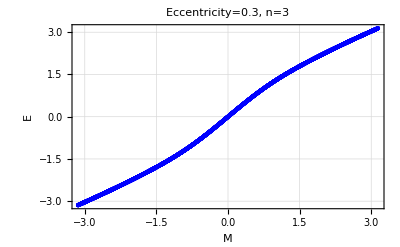

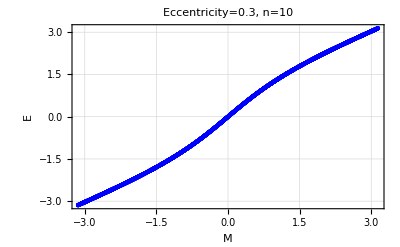

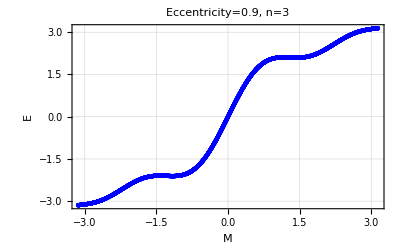

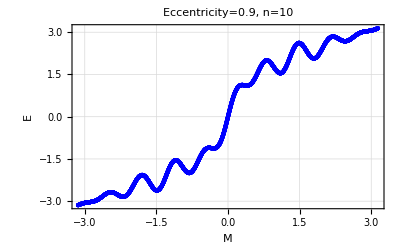

```mathematica
a=Table[l,{l,0.3,0.9,0.6}];    (* e = 0.3, 0.9 *)
g[x_]=x+Sum[a[[1]]^n/n!*D[(Sin[x])^n,{x,n-1}],{n,1,3}];   (* e=0.3 and n=3 *)
z[x_]=x+Sum[a[[1]]^n/n!*D[(Sin[x])^n,{x,n-1}],{n,1,10}] ; (* e=0.3 and n=10 *)
G[x_]=TrigReduce[g[x]];
Z[x_] = TrigReduce[z[x]];
Expand[G[x]];                           (* to anaptugma gia e=0.3 kai n=3*)
Expand[Z[x]];                           (* to anaptugma gia e=0.3 kai n=3*)

DATA = Table[x,{x,-Pi,Pi,0.001}];                               (* diamerhsh tou 2*pi *)

DATA1=Table[g[x],{x,-Pi,Pi,0.001}];
ListPlot[Transpose[{DATA,DATA1}],PlotStyle->Blue,AxesLabel->{"M","E"},PlotLabel->"Eccentricity=0.3, n=3",GridLines->Automatic, Frame->True]
DATA2=Table[z[x],{x,-Pi,Pi,0.001}];
ListPlot[Transpose[{DATA,DATA2}],PlotStyle->Blue,AxesLabel->{"M","E"},PlotLabel->"Eccentricity=0.3, n=10",GridLines->Automatic, Frame->True]

g1[x_]=x+Sum[a[[2]]^n/n!*D[(Sin[x])^n,{x,n-1}],{n,1,3}];    (* e=0.9 and n=3 *)
z1[x_]=x+Sum[a[[2]]^n/n!*D[(Sin[x])^n,{x,n-1}],{n,1,10}] ; (* e=0.9 and n=10 *)
G1[x_]=TrigReduce[g1[x]];
Z1[x_] = TrigReduce[z1[x]];
Expand[G1[x]];                            (* to anaptugma gia e=0.9 kai n=3*)
Expand[Z1[x]];                            (* to anaptugma gia e=0.9 kai n=10*)
  
DATA3=Table[g1[x],{x,-Pi,Pi,0.001}];
ListPlot[Transpose[{DATA,DATA3}],PlotStyle->Blue,AxesLabel->{"M","E"},PlotLabel->"Eccentricity=0.9, n=3",GridLines->Automatic, Frame->True]
DATA4=Table[z1[x],{x,-Pi,Pi,0.001}];
ListPlot[Transpose[{DATA,DATA4}],PlotStyle->Blue,AxesLabel->{"M","E"},PlotLabel->"Eccentricity=0.9, n=10",GridLines->Automatic, Frame->True]
```

Results: Clearly, for big eccentricities ( e.g.  e > 0.8 ), the graph becomes wave-like at the edges. I suppose that happens due to the fact that we have a power law of the eccentricity and more specificly, its polynomial character in combination with the trigonometric functions . Also, for increased order of the series the problem remains. Maybe this approximation works better for small eccentricities.

```mathematica
ClearAll["Global`*"]
```

Task 3: Fourier-Bessel expansion of E

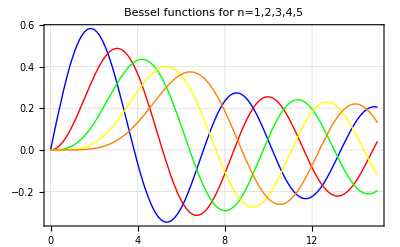

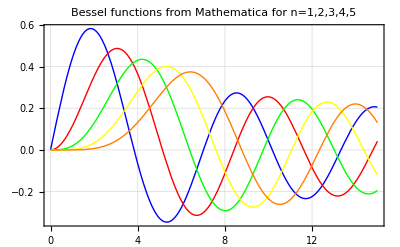

```mathematica
(*n=1;*)
J1[x_]=Sum[(-1)^k/(k!(n+k)!)*(x/2)^(n+2*k),{k,0,100},{n,1,1}];
J2[x_]=Sum[(-1)^k/(k!(n+k)!)*(x/2)^(n+2*k),{k,0,100},{n,2,2}];
J3[x_]=Sum[(-1)^k/(k!(n+k)!)*(x/2)^(n+2*k),{k,0,100},{n,3,3}];
J4[x_]=Sum[(-1)^k/(k!(n+k)!)*(x/2)^(n+2*k),{k,0,100},{n,4,4}];
J5[x_]=Sum[(-1)^k/(k!(n+k)!)*(x/2)^(n+2*k),{k,0,100},{n,5,5}];
J6[x_]=Sum[(-1)^k/(k!(n+k)!)*(x/2)^(n+2*k),{k,0,100},{n,6,6}];
J7[x_]=Sum[(-1)^k/(k!(n+k)!)*(x/2)^(n+2*k),{k,0,100},{n,7,7}];
J8[x_]=Sum[(-1)^k/(k!(n+k)!)*(x/2)^(n+2*k),{k,0,100},{n,8,8}];
J9[x_]=Sum[(-1)^k/(k!(n+k)!)*(x/2)^(n+2*k),{k,0,100},{n,9,9}];
J10[x_]=Sum[(-1)^k/(k!(n+k)!)*(x/2)^(n+2*k),{k,0,100},{n,10,10}];

p1=Plot[J1[x],{x,0,15},PlotStyle->Blue,GridLines->Automatic, Frame->True];
p2=Plot[J2[x],{x,0,15},PlotStyle->Red,GridLines->Automatic, Frame->True];
p3=Plot[J3[x],{x,0,15},PlotStyle->Green,GridLines->Automatic, Frame->True];
p4=Plot[J4[x],{x,0,15},PlotStyle->Yellow,GridLines->Automatic, Frame->True];
p5=Plot[J5[x],{x,0,15},PlotStyle->Orange,GridLines->Automatic, Frame->True];

Show[p1,p2,p3,p4,p5,PlotLabel->"Bessel functions for n=1,2,3,4,5"]

p11 = Plot[BesselJ[1,x],{x,0,15},PlotStyle->Blue,GridLines->Automatic, Frame->True];
p22 = Plot[BesselJ[2,x],{x,0,15},PlotStyle->Red,GridLines->Automatic, Frame->True];
p33 = Plot[BesselJ[3,x],{x,0,15},PlotStyle->Green,GridLines->Automatic, Frame->True];
p44 = Plot[BesselJ[4,x],{x,0,15},PlotStyle->Yellow,GridLines->Automatic, Frame->True];
p55 = Plot[BesselJ[5,x],{x,0,15},PlotStyle->Orange,GridLines->Automatic, Frame->True];

Show[p11,p22,p33,p44,p55,PlotLabel->"Bessel functions from Mathematica for n=1,2,3,4,5"]
```

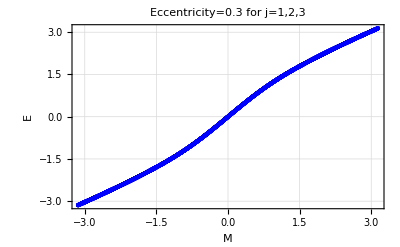

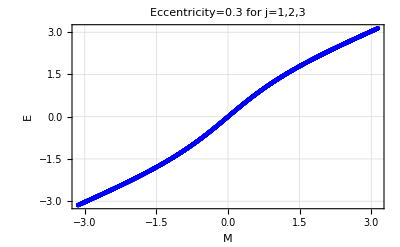

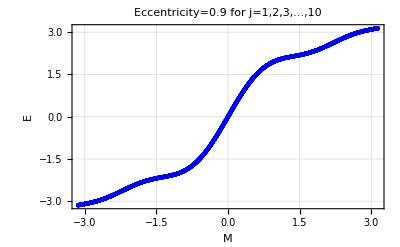

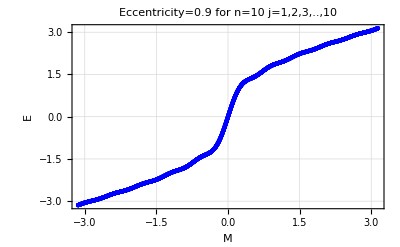

```mathematica
Jmatrix = {J1[1*e],J2[2*e],J3[3*e],J4[4*e],J5[5*e],J6[6*e],J7[7*e],J8[8*e],J9[9*e],J10[10*e]}; (* Jn *)
DATA = Table[x,{x,-Pi,Pi,0.001}];
Eanomaly[x_]= x + Sum[(2/j)*Jmatrix[[j]]*Sin[j*x]/. e->0.3,{j,1,3}];
DATA5=Table[Eanomaly[x],{x,-Pi,Pi,0.001}];
ListPlot[Transpose[{DATA,DATA5}],PlotStyle->Blue,AxesLabel->{"M","E"},PlotLabel->"Eccentricity=0.3 for j=1,2,3",GridLines->Automatic, Frame->True]

Eanomaly[x_]= x + Sum[(2/j)*Jmatrix[[j]]*Sin[j*x]/. e->0.3,{j,1,10}];
DATA6=Table[Eanomaly[x],{x,-Pi,Pi,0.001}];
ListPlot[Transpose[{DATA,DATA6}],PlotStyle->Blue,AxesLabel->{"M","E"},PlotLabel->"Eccentricity=0.3 for j=1,2,3",GridLines->Automatic, Frame->True]

Eanomaly[x_]= x + Sum[(2/j)*Jmatrix[[j]]*Sin[j*x]/. e->0.9,{j,1,3}];
DATA7=Table[Eanomaly[x],{x,-Pi,Pi,0.001}];
ListPlot[Transpose[{DATA,DATA7}],PlotStyle->Blue,AxesLabel->{"M","E"},PlotLabel->"Eccentricity=0.9 for j=1,2,3,...,10",GridLines->Automatic, Frame->True]

Eanomaly[x_]= x + Sum[(2/j)*Jmatrix[[j]]*Sin[j*x]/. e->0.9,{j,1,10}];
DATA8=Table[Eanomaly[x],{x,-Pi,Pi,0.001}];
ListPlot[Transpose[{DATA,DATA8}],PlotStyle->Blue,AxesLabel->{"M","E"},PlotLabel->"Eccentricity=0.9 for n=10 j=1,2,3,..,10",GridLines->Automatic, Frame->True]
```

```mathematica
ClearAll["Global`*"]
```

Results: We have better results than the Langrage’s method even for bigger eccentricities, but the order (j) must be increased.